```mathematica
SetDirectory["/Users/mgreuter/Documents/Research/histogram-voltage"];
```

## Model Development

### Symmetric, One-Site

```mathematica
Integrate[b^2/((x-a)^2+b^2),x]
```

-b ArcTan[(a-x)/b]

```mathematica
trans[e_,eps_,gamma_]:=gamma^2/((e-eps)^2+gamma^2);
conductance[V_,efermi_,eta_,eps_,gamma_]:=eta trans[efermi+eta V,eps,gamma]+(1-eta)trans[efermi+(eta-1) V,eps,gamma];
nondiffconductance[V_,efermi_,eta_,eps_,gamma_]:=gamma/V(ArcTan[(efermi+eta V-eps)/gamma]-ArcTan[(efermi+(eta-1)V-eps)/gamma]);
```

```mathematica
With[{z=efermi-eps},
FullSimplify[conductance[V,efermi,eta,eps,gamma]==(gamma^2(z+eta V)^2-2eta V gamma^2 (z+eta V)+eta V^2gamma^2+gamma^4)/((z+eta V)^4-2V(z+eta V)^3+(V^2+2gamma^2)(z+eta V)^2-2V gamma^2(z+eta V)+V^2gamma^2+gamma^4)]]
```

True

```mathematica
With[{z=efermi-eps},
FullSimplify[conductance[V,efermi,eta,eps,gamma]==(V^2eta(1-eta)gamma^2+gamma^2z^2+gamma^4)/((z+eta V)^4-2V(z+eta V)^3+(V^2+2gamma^2)(z+eta V)^2-2V gamma^2(z+eta V)+V^2gamma^2+gamma^4)]]
```

True

### Asymmetric, One-Site

```mathematica
Assuming[eps∈Reals&&gammaL>0&&gammaR>0,
Integrate[4gammaL gammaR/(4(z-eps)^2+(gammaL+gammaR)^2),z]]
```

-(2 gammaL gammaR ArcTan[(2 (eps-z))/(gammaL+gammaR)])/(gammaL+gammaR)

### Symmetric, One-Site, Voltage-Dependent

```mathematica
Assuming[g>0,
FullSimplify[
Integrate[z/(z^2+g^2)^2,z]]]
```

-1/(2 (g^2+z^2))

```mathematica
trans[V_,e_,eps_,gamma_]:=gamma^2 /((e-eps-V)^2+gamma^2);
conductance[V_,efermi_,eta_,eps_,gamma_]:=
(eta-1) trans[V,efermi+eta V,eps,gamma]+(2-eta) trans[V,efermi+(eta-1)V,eps,gamma];
nondiffconductance[V_,efermi_,eta_,eps_,gamma_]:=gamma/V(ArcTan[(efermi+(eta-1)V-eps)/gamma]-ArcTan[(efermi+(eta-2)V-eps)/gamma]);
```

### Symmetric, Two-Site

```mathematica
Assuming[gamma>0&&beta∈Reals&&beta≠0,
FullSimplify[Integrate[((4z^2-gamma^2-4beta^2)^2+16gamma^2 z^2)^(-1),z]]]
```

((-2 ⅈ beta+gamma) ArcTanh[(2 z)/(2 beta-ⅈ gamma)]+(2 ⅈ beta+gamma) ArcTanh[(2 z)/(2 beta+ⅈ gamma)])/(16 beta gamma (4 beta^2+gamma^2))

### Asymmetric, Two-Site

```mathematica
Assuming[gammaL>0&&gammaR>0&&beta∈Reals&&beta≠0,
FullSimplify[Integrate[((4z^2-gammaL gammaR-4beta^2)^2+4(gammaL+gammaR)^2 z^2)^(-1),z]]]//DisplayForm
```

(ArcTan[(2 √2 z)/(√(-8 beta^2+gammaL^2-gammaL √(-16 beta^2+(gammaL-gammaR)^2)-√(-16 beta^2+(gammaL-gammaR)^2) gammaR+gammaR^2))]/(√(-8 beta^2+gammaL^2-gammaL √(-16 beta^2+(gammaL-gammaR)^2)-√(-16 beta^2+(gammaL-gammaR)^2) gammaR+gammaR^2))-ArcTan[(2 √2 z)/(√(-8 beta^2+gammaL^2+gammaL √(-16 beta^2+(gammaL-gammaR)^2)+gammaR (√(-16 beta^2+(gammaL-gammaR)^2)+gammaR)))]/(√(-8 beta^2+gammaL^2+gammaL √(-16 beta^2+(gammaL-gammaR)^2)+gammaR (√(-16 beta^2+(gammaL-gammaR)^2)+gammaR))))/(√2 √(-16 beta^2+(gammaL-gammaR)^2) (gammaL+gammaR))

### Symmetric, Two-Site, Voltage-Dependent

```mathematica
T[z_]=Assuming[gamma∈Reals&&eps∈Reals&&beta∈Reals&&V∈Reals&&z∈Reals,
With[{
H={{eps-V/2,beta},{beta,eps+V/2}},
sigmaL={{-I gamma/2,0},{0,0}},
sigmaR={{0,0},{0,-I gamma/2}}
},
With[{
gammaL=I(sigmaL-ConjugateTranspose[sigmaL]),
gammaR=I(sigmaR-ConjugateTranspose[sigmaR])
},

Module[{G},
G=Inverse[z IdentityMatrix[2]-H-sigmaL-sigmaR];
FullSimplify[Tr[G.gammaL.ConjugateTranspose[G].gammaR]]
]]]]
```

(16 beta^2 gamma^2)/((4 beta^2-(2 eps+ⅈ gamma-V-2 z) (2 eps+ⅈ gamma+V-2 z)) (4 beta^2-4 eps^2+4 ⅈ eps gamma+gamma^2+V^2+8 eps z-4 ⅈ gamma z-4 z^2))

```mathematica
Assuming[gamma∈Reals&&eps∈Reals&&beta∈Reals&&V∈Reals&&z∈Reals,
FullSimplify[T[z]==16gamma^2beta^2/((4(z-eps)^2-4beta^2-gamma^2-V^2)^2+16gamma^2(z-eps)^2)]
]
```

True

```mathematica
Assuming[gamma>0&&eps∈Reals&&beta∈Reals&&beta≠0&&V∈Reals&&z∈Reals,
FullSimplify[Integrate[16gamma^2beta^2/((4(z-eps)^2-4beta^2-gamma^2-V^2)^2+16gamma^2(z-eps)^2),z]]
]
```

1/(√(4 beta^2+V^2))2 ⅈ beta^2 gamma (ArcTan[(2 (eps-z))/(√(-4 beta^2+gamma^2-V^2-2 ⅈ gamma √(4 beta^2+V^2)))]/(√(-4 beta^2+gamma^2-V^2-2 ⅈ gamma √(4 beta^2+V^2)))-ArcTan[(2 (eps-z))/(√(-4 beta^2+gamma^2-V^2+2 ⅈ gamma √(4 beta^2+V^2)))]/(√(-4 beta^2+gamma^2-V^2+2 ⅈ gamma √(4 beta^2+V^2))))

```mathematica
Assuming[gamma∈Reals&&eps∈Reals&&beta∈Reals&&V∈Reals&&z∈Reals,
FullSimplify[D[T[z],V]==64V gamma^2beta^2(4(z-eps)^2-4beta^2-gamma^2-V^2)/((4(z-eps)^2-4beta^2-gamma^2-V^2)^2+16gamma^2(z-eps)^2)^2]
]
```

True

```mathematica
Assuming[a∈Reals&&b∈Reals&&z∈Reals,
FullSimplify[Integrate[(4z^2-a)/((4z^2-a)^2+b z^2)^2,z]]]
```

1/(2 a)((z (-12 a+b+16 z^2))/((16 a-b) (a^2-8 a z^2+b z^2+16 z^4))+(2 √2 (32 ⅈ a+√(16 a-b) √b-ⅈ b) ArcTan[(4 √2 z)/(√(-8 a-ⅈ √(16 a-b) √b+b))])/((16 a-b)^(3/2) √b √(-8 a-ⅈ √(16 a-b) √b+b))+(2 √2 (-32 ⅈ a+√(16 a-b) √b+ⅈ b) ArcTan[(4 √2 z)/(√(-8 a+ⅈ √(16 a-b) √b+b))])/((16 a-b)^(3/2) √b √(-8 a+ⅈ √(16 a-b) √b+b)))

```mathematica
trans[V_,e_,eps_,beta_,gamma_]:=16gamma^2 beta^2/((4(e-eps)^2-4beta^2-gamma^2-V^2)^2+16gamma^2(e-eps)^2);

transderiv[V_,z_,beta_,gamma_]:=
With[{bv=4beta^2+V^2,atan=ArcTan[2z/(gamma-I Sqrt[4beta^2+V^2])]},

8V beta^2 gamma^2 z(4z^2+gamma^2-3bv)/(bv(bv+gamma^2)(16z^4+8(gamma^2-bv)z^2+(bv+gamma^2)^2))-8V gamma beta^2/(bv+gamma^2)^2Re[atan]-4V gamma^2beta^2(3bv+gamma^2)/((bv+gamma^2)^2bv^(3/2))Im[atan]];

conductance[V_,efermi_,eta_,eps_,beta_,gamma_]:=
eta trans[V,efermi+eta V,eps,beta,gamma]+(1-eta)trans[V,efermi+(eta-1)V,eps,beta,gamma]+transderiv[V,efermi-eps+eta V,beta,gamma]-transderiv[V,efermi-eps+(eta-1)V,beta,gamma];
```

```mathematica
nondiffintegral[V_,z_,beta_,gamma_]:=4beta^2gamma/(V Sqrt[4beta^2+V^2])Im[ArcTan[2z/(gamma-I Sqrt[4beta^2+V^2])]/(gamma-I Sqrt[4beta^2+V^2])];

nondiffconductance[V_,efermi_,eta_,eps_,beta_,gamma_]:=
nondiffintegral[V,efermi-eps+eta V,beta,gamma]-nondiffintegral[V,efermi-eps+(eta-1)V,beta,gamma];
```

### Asymmetric, Two-Site, Voltage-Dependent

```mathematica
Assuming[gammaL>0&&gammaR>0&&eps∈Reals&&beta∈Reals&&V∈Reals&&z∈Reals,
FullSimplify[
With[{
H={{eps-V/2,beta},{beta,eps+V/2}},
sigmaL={{-I gammaL/2,0},{0,0}},
sigmaR={{0,0},{0,-I gammaR/2}}
},
With[{
GammaL=I(sigmaL-ConjugateTranspose[sigmaL]),
GammaR=I(sigmaR-ConjugateTranspose[sigmaR])
},

Module[{G},
G=Inverse[z IdentityMatrix[2]-H-sigmaL-sigmaR];
FullSimplify[Tr[G.GammaL.ConjugateTranspose[G].GammaR]]
]]]==16gammaL gammaR beta^2/((4(z-eps)^2-4beta^2-V^2)^2+(4(z-eps)^2+V^2)(gammaL^2+gammaR^2)-4V(z-eps)(gammaL^2-gammaR^2)+8beta^2 gammaL gammaR+gammaL^2 gammaR^2)]]
```

True

```mathematica
Assuming[gammaL>0&&gammaR>0&&eps∈Reals&&beta∈Reals&&V∈Reals&&z∈Reals,
FullSimplify[
Integrate[16gammaL gammaR beta^2/((4(z-eps)^2-4beta^2-V^2)^2+(4(z-eps)^2+V^2)(gammaL^2+gammaR^2)-4V(z-eps)(gammaL^2-gammaR^2)+8beta^2 gammaL gammaR+gammaL^2 gammaR^2),z]]]
```

-4 beta^2 gammaL gammaR RootSum[16 beta^4+8 beta^2 gammaL gammaR+gammaL^2 gammaR^2+8 beta^2 V^2+gammaL^2 V^2+gammaR^2 V^2+V^4+4 gammaL^2 V #1-4 gammaR^2 V #1-32 beta^2 #1^2+4 gammaL^2 #1^2+4 gammaR^2 #1^2-8 V^2 #1^2+16 #1^4&,Log[eps-z-#1]/(gammaL^2 V-gammaR^2 V-16 beta^2 #1+2 gammaL^2 #1+2 gammaR^2 #1-4 V^2 #1+16 #1^3)&]

## Tests for the Code

If needed, h can be a function of v (lowercase)

```mathematica
CodeTest[h_,sigmaL_,sigmaR_,eta_,V_,EF_]:=
Module[{gammaL,gammaR,t,n},
n=Dimensions[h][[1]];

gammaL=I(sigmaL-ConjugateTranspose[sigmaL]);
gammaR=I(sigmaR-ConjugateTranspose[sigmaR]);

(* Get the transmission as a function of energy, z *)
t[z_]=Assuming[z∈Reals&&v∈Reals,FullSimplify[With[{G=Inverse[z IdentityMatrix[n]-h-sigmaL-sigmaR]},Tr[G.gammaL.ConjugateTranspose[G].gammaR]]]];

(* Zero-bias conductance *)
Print["Zero bias: "<>ToString[Re[t[EF]/.{v->V}]]];

(* Static conductance *)
Print["Static: "<>ToString[Re[(NIntegrate[t[z]/.{v->V},{z,EF+(eta-1)V,EF+eta V}]/V)]]];

(* Differential conductance *)
Print["Differential: "<>ToString[Re[((eta t[EF+eta V]+(1-eta)t[EF+(eta-1)V])/.{v->V})+NIntegrate[FullSimplify[(D[t[z],v])/.{v->V}],{z,EF+(eta-1)V,EF+eta V}]]]];
];
```

### Symmetric, One-Site

```mathematica
With[{eps=-4.,gamma=0.8,eta=0.5,V=1.,EF=0.},
CodeTest[{{eps}},{{-I gamma/2}},{{-I gamma/2}},eta,V,EF]]
```

Zero bias: 0.0384615

Static: 0.0390172

Differential: 0.0401438

```mathematica
With[{eps=-9.,gamma=0.4,eta=0.8,V=-0.4,EF=1.},
CodeTest[{{eps}},{{-I gamma/2}},{{-I gamma/2}},eta,V,EF]]
```

Zero bias: 0.00159744

Static: 0.00163709

Differential: 0.00167814

```mathematica
With[{eps=-17.,gamma=0.67,eta=0.14,V=1.4,EF=3.},
CodeTest[{{eps}},{{-I gamma/2}},{{-I gamma/2}},eta,V,EF]]
```

Zero bias: 0.00112099

Static: 0.00118115

Differential: 0.00124526

### Asymmetric, One-Site

```mathematica
With[{eps=-4.,gammaL=0.8,gammaR=1.0,eta=0.5,V=1.,EF=0.},
CodeTest[{{eps}},{{-I gammaL/2}},{{-I gammaR/2}},eta,V,EF]]
```

Zero bias: 0.0475907

Static: 0.0482617

Differential: 0.0496212

```mathematica
With[{eps=-9.,gammaL=0.4,gammaR=0.2,eta=0.8,V=-0.4,EF=1.},
CodeTest[{{eps}},{{-I gammaL/2}},{{-I gammaR/2}},eta,V,EF]]
```

Zero bias: 0.000799281

Static: 0.000819131

Differential: 0.000839689

```mathematica
With[{eps=-17.,gammaL=0.67,gammaR=1.98,eta=0.14,V=1.4,EF=3.},
CodeTest[{{eps}},{{-I gammaL/2}},{{-I gammaR/2}},eta,V,EF]]
```

Zero bias: 0.00330201

Static: 0.00347858

Differential: 0.00366672

### Symmetric, One-Site, Voltage-Dependent

```mathematica
With[{eps=-4.,gamma=0.8,eta=0.5,V=1.,EF=0.},
CodeTest[{{eps+v}},{{-I gamma/2}},{{-I gamma/2}},eta,V,EF]]
```

Zero bias: 0.06639

Static: 0.0679934

Differential: 0.114507

```mathematica
With[{eps=-9.,gamma=0.4,eta=0.8,V=-0.4,EF=1.},
CodeTest[{{eps+v}},{{-I gamma/2}},{{-I gamma/2}},eta,V,EF]]
```

Zero bias: 0.0014771

Static: 0.00151231

Differential: 0.00143116

```mathematica
With[{eps=-17.,gamma=0.67,eta=0.14,V=1.4,EF=3.},
CodeTest[{{eps+v}},{{-I gamma/2}},{{-I gamma/2}},eta,V,EF]]
```

Zero bias: 0.00129587

Static: 0.001371

Differential: 0.00166364

### Symmetric, Two-Site

```mathematica
With[{eps=-4.,gamma=0.8,eta=0.5,V=1.,EF=0.,beta=-3.},
CodeTest[{{eps,beta},{beta,eps}},{{-I gamma/2,0},{0,0}},{{0,0},{0,-I gamma/2}},eta,V,EF]]
```

Zero bias: 0.101007

Static: 0.127042

Differential: 0.186815

```mathematica
With[{eps=-3.,gamma=0.4,eta=0.8,V=-0.4,EF=1.,beta=-0.8},
CodeTest[{{eps,beta},{beta,eps}},{{-I gamma/2,0},{0,0}},{{0,0},{0,-I gamma/2}},eta,V,EF]]
```

Zero bias: 0.00043159

Static: 0.000494645

Differential: 0.000568266

```mathematica
With[{eps=1.1,gamma=0.67,eta=0.14,V=1.4,EF=3.,beta=-1.6},
CodeTest[{{eps,beta},{beta,eps}},{{-I gamma/2,0},{0,0}},{{0,0},{0,-I gamma/2}},eta,V,EF]]
```

Zero bias: 0.459683

Static: 0.560554

Differential: 0.230111

### Asymmetric, Two-Site

```mathematica
With[{eps=-4.,gammaL=0.8,gammaR=1.0,beta=-3.,eta=0.5,V=1.,EF=0.},
CodeTest[{{eps,beta},{beta,eps}},{{-I gammaL/2,0},{0,0}},{{0,0},{0,-I gammaR/2}},eta,V,EF]]
```

Zero bias: 0.121622

Static: 0.149936

Differential: 0.213248

```mathematica
With[{eps=-3.,gammaL=0.4,gammaR=0.2,beta=-0.8,eta=0.8,V=-0.4,EF=1.},
CodeTest[{{eps,beta},{beta,eps}},{{-I gammaL/2,0},{0,0}},{{0,0},{0,-I gammaR/2}},eta,V,EF]]
```

Zero bias: 0.000216257

Static: 0.000247897

Differential: 0.000284847

```mathematica
With[{eps=5.,gammaL=0.67,gammaR=1.98,beta=-1.6,eta=0.14,V=1.4,EF=-1.},
CodeTest[{{eps,beta},{beta,eps}},{{-I gammaL/2,0},{0,0}},{{0,0},{0,-I gammaR/2}},eta,V,EF]]
```

Zero bias: 0.00292927

Static: 0.00217835

Differential: 0.00164361

### Symmetric, Two-Site, Voltage-Dependent

```mathematica
With[{eps=-4.,gamma=0.8,eta=0.5,V=1.,EF=0.,beta=-3.},
CodeTest[{{eps-v/2,beta},{beta,eps+v/2}},{{-I gamma/2,0},{0,0}},{{0,0},{0,-I gamma/2}},eta,V,EF]]
```

Zero bias: 0.107326

Static: 0.136415

Differential: 0.222768

```mathematica
With[{eps=-3.,gamma=0.4,eta=0.8,V=-0.4,EF=1.,beta=-0.8},
CodeTest[{{eps-v/2,beta},{beta,eps+v/2}},{{-I gamma/2,0},{0,0}},{{0,0},{0,-I gamma/2}},eta,V,EF]]
```

Zero bias: 0.000433828

Static: 0.000497406

Differential: 0.000577222

```mathematica
With[{eps=1.1,gamma=0.67,eta=0.14,V=1.4,EF=3.,beta=-1.6},
CodeTest[{{eps-v/2,beta},{beta,eps+v/2}},{{-I gamma/2,0},{0,0}},{{0,0},{0,-I gamma/2}},eta,V,EF]]
```

Zero bias: 0.631062

Static: 0.457519

Differential: -0.0108761

## Look at Sample Data

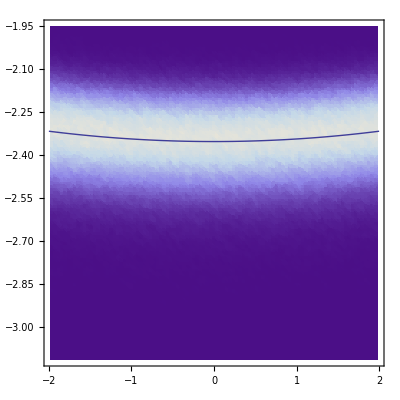

```mathematica
testdata=ReadList["/Users/mgreuter/Documents/Research/Codes/histogram-fitter/master/src/data",{Real,Real,Real}];
Show[ListDensityPlot[testdata],
Plot[Log[10,conductance[V,0.,0.5,-6.,0.4]],{V,-2,2}]]
```